# Boundary Conditions

```mathematica
MakeBoxes[ap,TraditionalForm]:="a_+";
MakeBoxes[am,TraditionalForm]:="a_-";
MakeBoxes[ep,TraditionalForm]:="e_-";
MakeBoxes[em,TraditionalForm]:="e_-";
MakeBoxes[vp,TraditionalForm]:="v_+";
MakeBoxes[vm,TraditionalForm]:="v_-";
MakeBoxes[wp,TraditionalForm]:="w_+";
MakeBoxes[wm,TraditionalForm]:="w_-";
MakeBoxes[γp,TraditionalForm]:="γ_+";
MakeBoxes[γm,TraditionalForm]:="γ_-";
MakeBoxes[pp,TraditionalForm]:="p_+";
MakeBoxes[pm,TraditionalForm]:="p_-";
MakeBoxes[Tp,TraditionalForm]:="T_+";
MakeBoxes[Tm,TraditionalForm]:="T_-";
MakeBoxes[αp,TraditionalForm]:="α_+";
MakeBoxes[αm,TraditionalForm]:="α_-";
MakeBoxes[ϵp,TraditionalForm]:="ϵ_+";
MakeBoxes[ϵm,TraditionalForm]:="ϵ_-";
```

```mathematica
$Assumptions={};
```

```mathematica
eqns={vp vm ==(1-(1-3αp)r)/(3-3(1+αp)r),vp/vm==(3+(1-3αp)r)/(1+3(1+αp)r)};
eqns/.{αp->(ϵp-ϵm)/(ap Tp^4),r->(ap Tp^4)/(am Tm^4)}/.{ap->-3/(4 Tp^3)D[Veff[T],T]/.{T->Tp},am->-3/(4 Tm^3)D[Veff[T],T]/.{T->Tm},ϵp->(Veff[Tp]+-Tp/4 D[Veff[T],T]/.{T->Tp}),ϵm->(Veff[Tm]+-Tm/4 D[Veff[T],T]/.{T->Tm})}//Simplify
eqnbag=eqns/.{αp->ϵ/(ap Tp^4),r->(ap Tp^4)/(am Tm^4)}//Simplify (*Assuming perfect bag model*)
```

{v_- v_+==(Veff(T_-)-Veff(T_+))/(T_- Veff'(T_-)-Veff(T_-)-T_+ Veff'(T_+)+Veff(T_+)),(v_+)/(v_-)==(T_- Veff'(T_-)-Veff(T_-)+Veff(T_+))/(Veff(T_-)+T_+ Veff'(T_+)-Veff(T_+))}

{v_- v_+==(a_- (T_-)^4-a_+ (T_+)^4+3 ϵ)/(3 a_- (T_-)^4-3 (a_+ (T_+)^4+ϵ)),(v_+)/(v_-)==(3 a_- (T_-)^4+a_+ (T_+)^4-3 ϵ)/(a_- (T_-)^4+3 a_+ (T_+)^4+3 ϵ)}

```mathematica
eqnbag[[1]]
```

v_- v_+==(a_- (T_-)^4-a_+ (T_+)^4+3 ϵ)/(3 a_- (T_-)^4-3 (a_+ (T_+)^4+ϵ))

```mathematica
(3+(1-3αp)r)/(1+3(1+αp)r)/.{αp->(ϵp-ϵm)/(ap Tp^4),r->(ap Tp^4)/(am Tm^4)}/.num/.{Tp->80,vp->0.7,ϵp->10^7,ϵm->0}/.{Tm->81}//Simplify
```

0.970015

## Try to solve the boundary equations in the perfect bag model

First test the SM case with arbitrary parameter.

```mathematica
num={am->106.75-7/8*12,ap->106.75};
```

### Detonation

```mathematica
NSolve[(eqnbag/.num/.{vp->0.7,Tp->80,ϵ->10^7}),{vm,Tm},PositiveReals]
```

{{v_-→0.694703,T_-→82.5502},{v_-→0.479822,T_-→100.008}}

```mathematica
sol=NSolve[(eqnbag/.num/.{vp->0.7,Tp->80,ϵ->10^7}),{vm,Tm},PositiveReals][[1]];
```

```mathematica
h[z_]:=1/2(1-Tanh[z]);
```

```mathematica
Solve[h[]]
```

### Deflagration

```mathematica
μ[x_,v_]=(x-v)/(1-x v);
```

```mathematica
Deqns={2 v[x]/x==1/(1-v[x]^2)(1-v[x]x)(μ[x,v[x]]^2/(1/3)-1)v'[x],T'[x]==T[x] 1/(1-v[x]^2)μ[x,v[x]] v'[x]};
```

Try to solve: v_w=0.5, T_n=60 GeV. Remember in deflagration we have v_->v_+.

```mathematica
vw=0.5;
sol=NSolve[(eqnbag/.num/.{vm->vw,Tm->59,ϵ->10^8}),{vp,Tp},PositiveReals][[2]]
```

{v_+→0.354205,T_+→65.1206}

We should first solve the velocity profile. Use energy budget paper Eq 33.

```mathematica
{vsol[τ_],ξsol[τ_]}={v[τ],ξ[τ]}/.NDSolve[{v'[τ]==2 v[τ] 1/3(1-v[τ]^2)(1-ξ[τ]v[τ]),ξ'[τ]==ξ[τ]((ξ[τ]-v[τ])^2-1/3(1-ξ[τ]v[τ])^2),(ξ[10]==vw),v[10]==μ[vw,vp]/.sol},{v[τ],ξ[τ]},{τ,0.01,10}][[1]]
```

{InterpolatingFunction[…](τ),InterpolatingFunction[…](τ)}

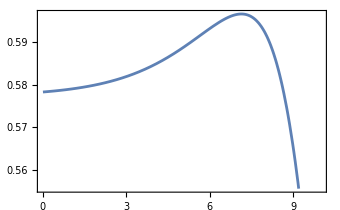

```mathematica
Plot[ξsol[x],{x,0.01,10}]
```

The ξ here is not a monotonic function as shown in energy budget paper in Fig.2. This is exactly the reason why we should not solve v as a function of ξ directly: ξ has a maximum. We should find the maximum at first.

```mathematica
τmin=x/.FindMaximum[ξsol[x],{x,6.69}][[2]]
ξmax=FindMaximum[ξsol[x],{x,6.69}][[1]]
```

InterpolatingFunction::dmval: Input value {83.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

7.14509

InterpolatingFunction::dmval: Input value {83.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.59656

I don’t know why output so many warnings. Actually nothing is outside the solution region...

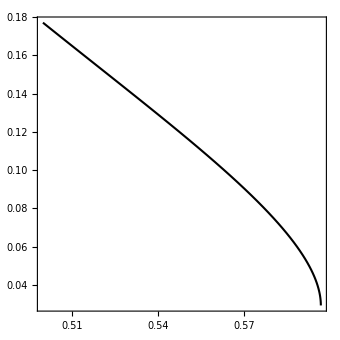

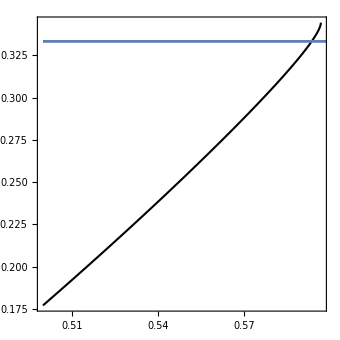

```mathematica
ParametricPlot[{ξsol[τ],vsol[τ]},{τ,τmin,10},AspectRatio->1,PlotRange->Full]
Show[ParametricPlot[{ξsol[τ],μ[ξsol[τ],vsol[τ]]ξsol[τ]},{τ,τmin,10},AspectRatio->1,PlotRange->Full],Plot[1/3,{x,0.5,0.7}]]
```

Now we have the maximum of ξ. Solve in this range.

```mathematica
{Tsol[x_],vsol[x_]}={T[x],v[x]}/.NDSolve[Join[Deqns,{(v[vw]==μ[0.5,vp]/.sol),(T[vw]==Tp/.sol)}],{T[x],v[x]},{x,vw,ξmax*0.9999}][[1]]
```

{InterpolatingFunction[…](x),InterpolatingFunction[…](x)}

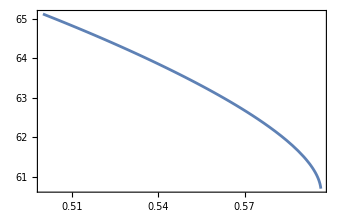

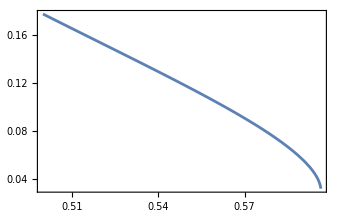

```mathematica
Plot[Tsol[x],{x,0.5,ξmax*0.9999}]
Plot[vsol[x],{x,0.5,ξmax*0.9999}]
```

Find the shock front.

```mathematica
xsh=x/.FindRoot[μ[x,vsol[x]]x==1/3,{x,0.55}]
```

InterpolatingFunction::dmval: Input value {0.59824} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.597655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.597143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.593373

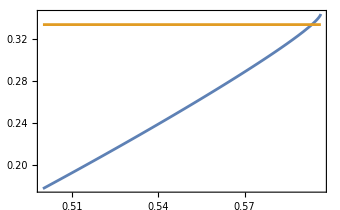

```mathematica
Plot[{μ[x,vsol[x]]x,1/3},{x,0.5,ξmax*0.9999}]
```

The temperature at the shock wave front should be

```mathematica
Tsol[xsh]
```

61.2472

```mathematica
find‵Tsh[Tmnum_]:=(
sol=Select[{vp,Tp}/.NSolve[(eqnbag/.num/.{vm->vw,Tm->Tmnum,ϵ->10^8}),{vp,Tp},PositiveReals],#[[1]]<1/(√3)&][[1]];
{vsol[τ_],ξsol[τ_]}={v[τ],ξ[τ]}/.NDSolve[{v'[τ]==2 v[τ] 1/3(1-v[τ]^2)(1-ξ[τ]v[τ]),ξ'[τ]==ξ[τ]((ξ[τ]-v[τ])^2-1/3(1-ξ[τ]v[τ])^2),(ξ[10]==vw),v[10]==μ[vw,sol[[1]]]},{v[τ],ξ[τ]},{τ,0.01,10}][[1]];
τmin=x/.FindMaximum[ξsol[x],{x,6.69}][[2]];
ξmax=FindMaximum[ξsol[x],{x,6.69}][[1]];
{Tsol[x_],vsol[x_]}={T[x],v[x]}/.NDSolve[Join[Deqns,{(v[vw]==μ[0.5,sol[[1]]]),(T[vw]==sol[[2]])}],{T[x],v[x]},{x,vw,ξmax*0.9999}][[1]];
xsh=x/.FindRoot[μ[x,vsol[x]]x==1/3,{x,0.55}];
Return[Tsol[xsh]];
)
```

```mathematica
find‵Tsh[59]
```

InterpolatingFunction::dmval: Input value {83.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

61.2472

```mathematica
Tmax=60;
Tmin=57;
For[i=0,i<30,i++,
Tcalculate=(Tmax+Tmin)/2;
Tsh=find‵Tsh[Tcalculate];
If[Tsh<60,Tmin=Tcalculate,Tmax=Tcalculate];
]
```

InterpolatingFunction::dmval: Input value {83.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

```mathematica
Tcalculate//N
```

57.464

```mathematica
find‵Tsh[Tcalculate]
```

InterpolatingFunction::dmval: Input value {83.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

60.